NAME : PARTH KUMAR SINGH
COLLEGE ROLL NO.: 2232139
UNIVERSITY ROLL NO.: 22036563034
COURSE : B.Sc. (Hons.) Mathematics/Year3/Complex Analysis
SECTION : A

PRACTICAL 6 : Show that image of the half plane {z: Re[z] >= 1/2 } under the linear transformation ω=f(z)=1/2 is the disk {ω: |ω - 1| < 1}

```mathematica
z=x+ⅈ*y
```

x+ⅈ y

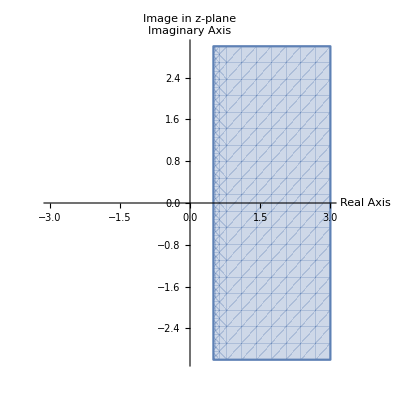

```mathematica
a=RegionPlot[
Re[z]>=1/2,{x,-3,3},{y,-3,3},Axes->True,Frame->False,
AxesLabel->{"Real Axis","Imaginary Axis"},PlotLabel->"Image in z-plane"
]
```

```mathematica
f[z_]:=1/z
```

```mathematica
ω=ComplexExpand[f[z]]
```

x/(x^2+y^2)-(ⅈ y)/(x^2+y^2)

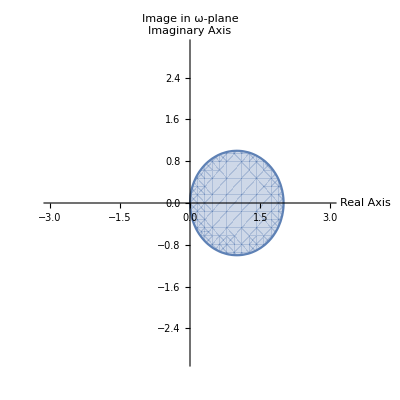

```mathematica
b=RegionPlot[
Re[1/z]>=1/2,{x,-3,3},{y,-3,3},Axes->True,Frame->False,
AxesLabel->{"Real Axis","Imaginary Axis"},PlotLabel->"Image in ω-plane"
]
```

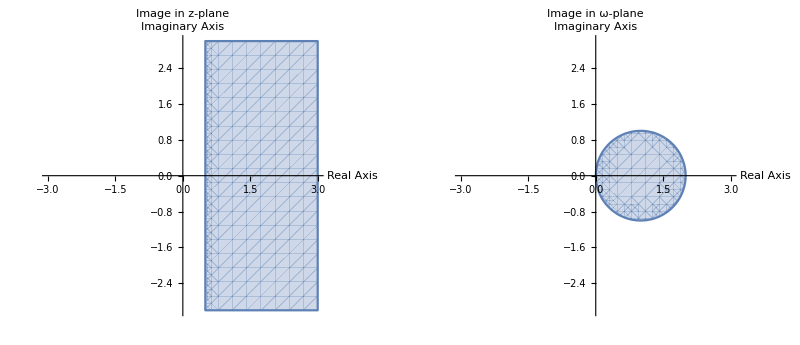

```mathematica
GraphicsRow[{a,b},Frame->All]
```